```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian System eta Data\\eta_0_beta_vary_omega_5"];

LNDatabeta075=ReadList["LNData_NM_beta_0.75.txt"];
LNDatabeta076=ReadList["LNData_NM_beta_0.76.txt"];
LNDatabeta077=ReadList["LNData_NM_beta_0.77.txt"];
LNDatabeta078=ReadList["LNData_NM_beta_0.78.txt"];
LNDatabeta079=ReadList["LNData_NM_beta_0.79.txt"];
LNDatabeta080=ReadList["LNData_NM_beta_0.8.txt"];
LNDatabeta081=ReadList["LNData_NM_beta_0.81.txt"];
LNDatabeta082=ReadList["LNData_NM_beta_0.82.txt"];
LNDatabeta083=ReadList["LNData_NM_beta_0.83.txt"];
LNDatabeta084=ReadList["LNData_NM_beta_0.84.txt"];
LNDatabeta085=ReadList["LNData_NM_beta_0.85.txt"];
```

```mathematica
MeanBetaData={
{0.75, Mean[Table[LNDatabeta075[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.76, Mean[Table[LNDatabeta076[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.77, Mean[Table[LNDatabeta077[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.78, Mean[Table[LNDatabeta078[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.79, Mean[Table[LNDatabeta079[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.80, Mean[Table[LNDatabeta080[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.81, Mean[Table[LNDatabeta081[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.82, Mean[Table[LNDatabeta082[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.83, Mean[Table[LNDatabeta083[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.84, Mean[Table[LNDatabeta084[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.85, Mean[Table[LNDatabeta085[[1]][[pt]][[2]], {pt, 100, 1001}]]}
};
```

```mathematica
(* LN12 and LN34 Data *)
LNBetaData={
{LNDatabeta075[[1]], LNDatabeta075[[6]], 0.75},
{LNDatabeta076[[1]], LNDatabeta076[[6]], 0.76},
{LNDatabeta077[[1]], LNDatabeta077[[6]], 0.77},
{LNDatabeta078[[1]], LNDatabeta078[[6]], 0.78},
{LNDatabeta079[[1]], LNDatabeta079[[6]], 0.79},
{LNDatabeta080[[1]], LNDatabeta080[[6]], 0.80},
{LNDatabeta081[[1]], LNDatabeta081[[6]], 0.81},
{LNDatabeta082[[1]], LNDatabeta082[[6]], 0.82},
{LNDatabeta083[[1]], LNDatabeta083[[6]], 0.83},
{LNDatabeta084[[1]], LNDatabeta084[[6]], 0.84},
{LNDatabeta085[[1]], LNDatabeta085[[6]], 0.85}};
```

```mathematica
(* Plotting Properties *)
width=600;
height=300;
PlotFormat1={LabelStyle->Directive[18], BaseStyle->"Latin Modern Roman", ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width};
LabelingInfo1={AxesLabel->{"β", "Saturated ℒ𝒩_12"}, PlotLabel->"n=4, β, η=0, m=1, ω=5, Ω=5, γ=0.5"};
LabelingInfo2={AxesLabel->{"τ", "ℒ𝒩"}};
```

```mathematica
(* LN12 and LN34 Plot as a function of β *)
LNBetaPlots=Table[ListPlot[{LNBetaData[[betavalue]][[1]], LNBetaData[[betavalue]][[2]]}, Joined->True, Evaluate[PlotFormat1], Evaluate[LabelingInfo2], PlotLabel->"n=4, β="<>ToString[LNBetaData[[betavalue]][[3]]]<>", η=0, m=1, ω=5, Ω=5, γ=0.5}"], {betavalue, 1, Length[LNBetaData]}];
ListAnimate[LNBetaPlots, AnimationRunning->False, ControlPlacement->Bottom]
```

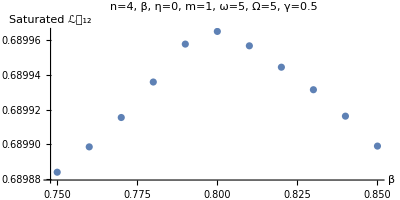
-Graphics--Graphics-

```mathematica
(* Points *)
MeanBetaDataptPlot=ListPlot[Table[MeanBetaData[[betavalue]], {betavalue, 1, Length[MeanBetaData]}], Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1], PlotRange->All];
(* Plot only Points of where suspected Max is *)
MeanBetaDataptPlotZoom=ListPlot[MeanBetaData[[1;;11]], Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Show Side by Side *)
Row[{MeanBetaDataptPlot, MeanBetaDataptPlotZoom}]
```

```mathematica
(* Reassign MeanBetaData *)
MeanBetaData={
{0.75, Mean[Table[LNDatabeta075[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.76, Mean[Table[LNDatabeta076[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.77, Mean[Table[LNDatabeta077[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.78, Mean[Table[LNDatabeta078[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.79, Mean[Table[LNDatabeta079[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.80, Mean[Table[LNDatabeta080[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.81, Mean[Table[LNDatabeta081[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.82, Mean[Table[LNDatabeta082[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.83, Mean[Table[LNDatabeta083[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.84, Mean[Table[LNDatabeta084[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.85, Mean[Table[LNDatabeta085[[1]][[pt]][[2]], {pt, 100, 1001}]]}};

(* Points *)
(* MeanBetaDataptPlot=ListPlot[Table[MeanBetaData[[betavalue]], {betavalue, 1, Length[MeanBetaData]}], Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];*)
(* Plot only Points of where suspected Max is *)
MeanBetaDataptPlotZoom=ListPlot[MeanBetaData, Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]]
(* Show Side by Side *)
(* Row[{MeanBetaDataptPlot, MeanBetaDataptPlotZoom}] *)
```

-Graphics-

InterpolatingFunction[…]

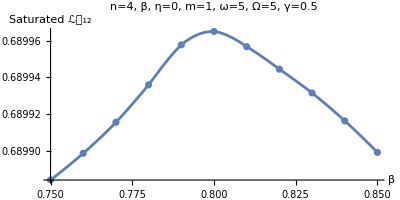

```mathematica
(* Interpolation: Must zoom in to where the suspected maximum is. *)
iMeanBetafunc=Interpolation[MeanBetaData[[1;;11]]]
iMeanBetaDatalinePlot=Plot[iMeanBetafunc[x], {x, 0.75, 0.85}, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Show together *)
Show[iMeanBetaDatalinePlot, MeanBetaDataptPlotZoom]
```

```mathematica
(* Take the derivative of the Interpolation Function *)
derivfunc[β_]:=D[iMeanBetafunc[x], x]/.x->β
```

{0.799794,0.689965}

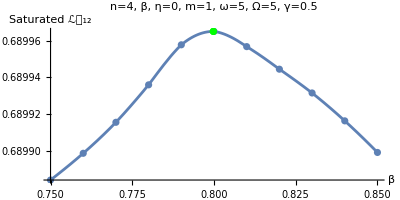

```mathematica
(* Calculating the value of the derivative of Interpolation Function near the maximum. Get start and end values from the graph. *)
start= 0.795;
end=0.805;
deridata=Table[{β, derivfunc[β]}, {β, start, end, 10^-6}];

(* Finding Optimum β for when Ω=ω=2 *)
βmax={};
Table[If[deridata[[value]][[2]]>0 && deridata[[value+1]][[2]]<0, AppendTo[βmax, Mean[{deridata[[value]][[1]],deridata[[value+1]][[1]]}]]], {value, 1, Length[deridata]-1}];
optimumpt=Flatten[{βmax, iMeanBetafunc[βmax]}]

(* Plot {βmax, Saturated LN12} *)
optimumptPlot=ListPlot[{optimumpt}, Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1], PlotStyle->Green];
Show[iMeanBetaDatalinePlot, MeanBetaDataptPlotZoom, optimumptPlot]
```